```mathematica
zbar = 1 +(6(1-FIS)-(1+FIS))/(1+FIS) μ/(8 sa)
varT = 2/(6(1-FIS)-(1+FIS))(zbar^2-1) // FullSimplify
```

1+((-1+6 (1-FIS)-FIS) μ)/(8 (1+FIS) sa)

(μ (16 (1+FIS) sa+(5-7 FIS) μ))/(32 (1+FIS)^2 sa^2)

```mathematica
σ2 = Log[varT/zbar^2+1]
SkewLogNormal = (Exp[σ2]+2)Sqrt[Exp[σ2]−1] // FullSimplify
```

Log[1+(μ (16 (1+FIS) sa+(5-7 FIS) μ))/(32 (1+FIS)^2 sa^2 (1+((-1+6 (1-FIS)-FIS) μ)/(8 (1+FIS) sa))^2)]

(√2 √((μ (16 (1+FIS) sa+(5-7 FIS) μ))/(8 (1+FIS) sa+(5-7 FIS) μ)^2) (192 (1+FIS)^2 sa^2-16 (1+FIS) (-17+21 FIS) sa μ+(-5+7 FIS) (-17+21 FIS) μ^2))/(8 (1+FIS) sa+(5-7 FIS) μ)^2

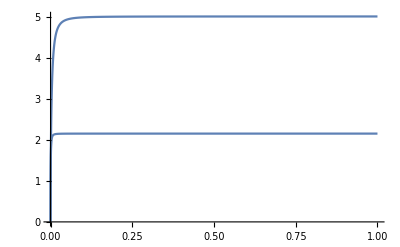

```mathematica
Plot[SkewLogNormal /. sa-> 0.001 /. FIS-> {0, 0.5}, {μ, 0, 1}]
```

-6+(3 (64 (1+FIS)^2 sa^2-112 (-1+FIS^2) sa μ+7 (-1+FIS) (-5+7 FIS) μ^2)^2)/(8 (1+FIS) sa+(5-7 FIS) μ)^4+(2 (64 (1+FIS)^2 sa^2-112 (-1+FIS^2) sa μ+7 (-1+FIS) (-5+7 FIS) μ^2)^3)/(8 (1+FIS) sa+(5-7 FIS) μ)^6+((64 (1+FIS)^2 sa^2-112 (-1+FIS^2) sa μ+7 (-1+FIS) (-5+7 FIS) μ^2)^4)/(8 (1+FIS) sa+(5-7 FIS) μ)^8

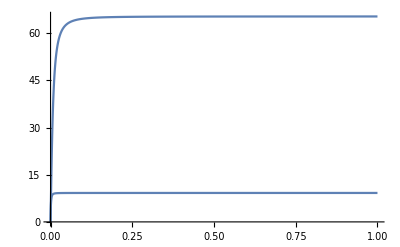

```mathematica
KurtosisLogNormal = 1Exp[4σ2]+2Exp[3σ2]+3Exp[2σ2]-6 // FullSimplify
Plot[KurtosisLogNormal /. sa-> 0.001 /. FIS-> {0.0, 0.5}, {μ, 0, 1}]
```

```mathematica
(Exp[B]+2)Sqrt[Exp[B]−1] /. B->Log[A]// FullSimplify
```

√(-1+A) (2+A)